```mathematica
凹面镜对平行光的折射
```

```mathematica
正入射
```

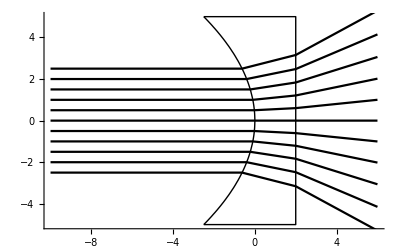

```mathematica
q=0.1;a=2.0;h=5.0;zm=-10.0;
n1=1;n2=2;n3=1;optical={};
Do[
p1={zm,y0};p2={-q y0^2,y0};
k1={1,0};
k=(n1 k1[[2]] (k1[[1]]+2 q p2[[2]] k1[[2]])
+2 q p2[[2]] (n2-n1))/
(n1 k1[[1]] (k1[[1]]+2 q p2[[2]] k1[[2]])
+n2-n1);
z3=a;y3=p2[[2]]+k (z3-p2[[1]]);
p3={z3,y3};
kz=1/√(1+k^2);ky=k kz;
k2={kz,ky};k=(n2 k2[[1]] k2[[2]])/(n3-n2+n2 k2[[1]]^2);
z4=3a;y4=p3[[2]]+k (z4-p3[[1]]);
p4={z4,y4};
g=Graphics[{Thickness[0.004],
Line[{p1,p2,p3,p4}]}];
AppendTo[optical,g],
{y0,-h/2,h/2,h/10}]
g=ContourPlot[z+q y^2==0,{z,-q h^2,2a},
{y,-h,h},ContourStyle->Thick];
AppendTo[optical,g];
g=Graphics[
{Thick,Line[{{-q h^2,h},{a,h},{a,-h},
{-q h^2,-h}}]}];
AppendTo[optical,g];
Show[optical,Axes->True,
AxesStyle->Thickness[0.003],
PlotRange->{{zm,z4},{-h,h}}]
Clear[optical,g,p1,p2,p3,p4]
```

```mathematica
斜入射
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

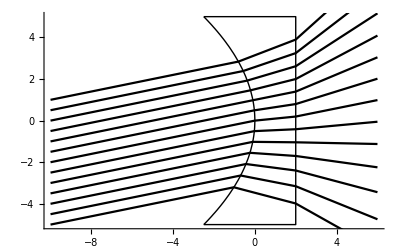

```mathematica
q=0.1;a=2.0;h=5.0;zm=-10.0;
n1=1;n2=2;n3=1;optical={};k0=0.2;
kz=1/√(1+k0^2);ky=k0 kz;
k1={kz,ky};
Do[
p1={zm,y0};
equ={y-y0==k0 (z-zm),q y^2+z==0};
s=Solve[equ,{z,y}];
m=z/.s;s=Select[s,(z/.#)==Max[m]&];
p2={z,y}/.s[[1]];
k=(n1 k1[[2]] (k1[[1]]+2 q p2[[2]] k1[[2]])
+2 q p2[[2]] (n2-n1))/
(n1 k1[[1]] (k1[[1]]+2 q p2[[2]] k1[[2]])
+n2-n1);
z3=a;y3=p2[[2]]+k (z3-p2[[1]]);
p3={z3,y3};
kz=1/√(1+k^2);ky=k kz;
k2={kz,ky};k=(n2 k2[[1]] k2[[2]])/(n3-n2+n2 k2[[1]]^2);
z4=3a;y4=p3[[2]]+k (z4-p3[[1]]);
p4={z4,y4};
g=Graphics[{Thickness[0.004],
Line[{p1,p2,p3,p4}]}];
AppendTo[optical,g],
{y0,-h,h/4,h/10}]
g=ContourPlot[z+q y^2==0,{z,-q h^2,2a},
{y,-h,h},ContourStyle->Thick];
AppendTo[optical,g];
g=Graphics[
{Thick,Line[{{-q h^2,h},{a,h},{a,-h},
{-q h^2,-h}}]}];
AppendTo[optical,g];
Show[optical,Axes->True,
AxesStyle->Thickness[0.003],
PlotRange->{{zm,z4},{-h,h}}]
Clear[optical,g,p1,p2,p3,p4]
```

```mathematica
三棱镜对平行光的折射
```

```mathematica
平行光入射
```

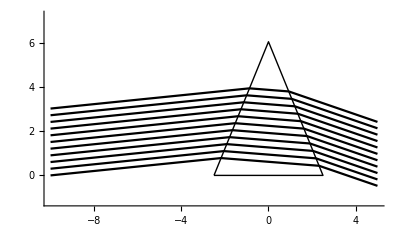

```mathematica
a=5.0;α=π/4.0;h=a Cot[α/2]/2;
zm=-2a;k0=0.1;
n1=1;n2=1.5;n3=1;optical={};
kz=1/√(1+k0^2);ky=k0 kz;k1={kz,ky};
Do[
p1={zm,y0};
equ1={y-y0==k0 (z-zm),y==Cot[α/2] (z+a/2)};
s=Solve[equ1,{z,y}];
p2={z,y}/.s[[1]];
k=
((n2-n1)+(k1[[2]]-Cot[α/2] k1[[1]])n1 k1[[2]])
/(Cot[α/2] (n1-n2)+
(k1[[2]]-Cot[α/2] k1[[1]]) n1 k1[[1]]);
equ2={y==p2[[2]]+k (z-p2[[1]]),
y==-Cot[α/2] (z-a/2)};
s=Solve[equ2,{z,y}];
p3={z,y}/.s[[1]];
kz=1/√(1+k^2);ky=k kz;k2={kz,ky};
k=
((n3-n2)+(k2[[2]]+Cot[α/2] k2[[1]])n2 k2[[2]])
/(Cot[α/2] (n3-n2)
+(k2[[2]]+Cot[α/2] k2[[1]])n2 k2[[1]]);
z4=a;y4=p3[[2]]+k (z4-p3[[1]]);
p4={z4,y4};
g=Graphics[{Thickness[0.004],
Line[{p1,p2,p3,p4}]}];
AppendTo[optical,g],
{y0,0,h/2,h/20}]
g=Graphics[
{Thick,Line[{{-a/2,0},{0,h},{a/2,0},
{-a/2,0}}]}];
AppendTo[optical,g];
Show[optical,Axes->True,
AxesStyle->Thickness[0.003],
PlotRange->{{zm,z4},{-0.2h,1.2h}}]
Clear[optical,g,p1,p2,p3,p4]
```

```mathematica
点光源入射
```

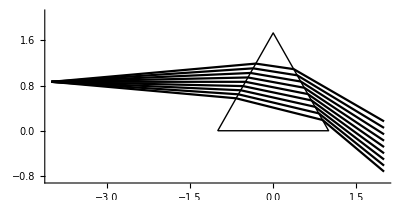

```mathematica
a=2.0;α=π/3;h=a Cot[α/2]/2;
zm=-2a;θm=5 π/180.0;
n1=1;n2=1.5;n3=1;optical={};
p1={zm,h/2};
Do[
k=Tan[θ];
kz=1/√(1+k^2);ky=k kz;k1={kz,ky};
equ={y-p1[[2]]==k(z-p1[[1]]),
y==Cot[α/2](z+a/2)};
s=Solve[equ,{z,y}];
p2={z,y}/.s[[1]];
k=
((n2-n1)+(k1[[2]]-Cot[α/2]k1[[1]])n1 k1[[2]])
/(Cot[α/2](n1-n2)
+(k1[[2]]-Cot[α/2]k1[[1]])n1 k1[[1]]);
equ={y==p2[[2]]+k (z-p2[[1]]),
y==-Cot[α/2](z-a/2)};
s=Solve[equ,{z,y}];
p3={z,y}/.s[[1]];
kz=1/√(1+k^2);ky=k kz;k2={kz,ky};
k=
((n3-n2)+(k2[[2]]+Cot[α/2]k2[[1]])n2 k2[[2]])
/(Cot[α/2](n3-n2)
+(k2[[2]]+Cot[α/2]k2[[1]])n2 k2[[1]]);
z4=a;y4=p3[[2]]+k (z4-p3[[1]]);
p4={z4,y4};
g=Graphics[{Thickness[0.004],
Line[{p1,p2,p3,p4}]}];
AppendTo[optical,g],
{θ,-θm,θm,θm/4}]
g=Graphics[
{Thick,Line[{{-a/2,0},{0,h},{a/2,0},
{-a/2,0}}]}];
AppendTo[optical,g];
Show[optical,Axes->True,
AxesStyle->Thickness[0.003],
PlotRange->{{zm,z4},{-0.5h,1.2h}}]
Clear[optical,g,p1,p2,p3,p4]
```